```mathematica
SetOptions[$FrontEnd,ShowCodeAssist->False]
Off[ClebschGordan::phy]
Off[NIntegrate::slwcon]
```

Symbolic tensor coupling and product

```mathematica
coup::usage="two spherical tensors  a⃗,b⃗ (arg_(4, 5)) are coupled to an eigenstate of s_1+s_2=J (arg_(1, 2, 3))\nInput: (s_1,s_2,J,a⃗,b⃗)\nOutput: {[a⊗b]^JJ,…,[a⊗b]^(J - J)}"
```

two spherical tensors  a⃗,b⃗ (arg_(4, 5)) are coupled to an eigenstate of s_1+s_2=J (arg_(1, 2, 3))
Input: (s_1,s_2,J,a⃗,b⃗)
Output: {[a⊗b]^JJ,…,[a⊗b]^(J - J)}

```mathematica
coup[s1_,s2_,J_,a_,b_]:=(
mAndm=Tuples[{Range[-s1,s1],Range[-s2,s2]}];
mAndmR=Table[Select[mAndm,ClebschGordan[{s1,#[[1]]},{s2,#[[2]]},{J,-M}]!=0&],{M,-J,J}];
Table[Table[ClebschGordan[{s1,m[[1]]},{s2,m[[2]]},{J,-M}] (a[[(s1+1)-m[[1]]]]) (b[[(s2+1)-m[[2]]]]),{m,mAndmR[[J+1+M]]}]/.List->Plus,{M,-J,J}]
(*Table[Sum[ClebschGordan[{s1,m[[1]]},{s2,m[[2]]},{J,-M}] a[[(s1+1)-m[[1]]]] b[[(s2+1)-m[[2]]]],{m,mAndmR[[J+1+M]]}],{M,-J,J}]*)
)
```

```mathematica
spinprod::usage="arg_1 is a sum of products of single-particle spin functions and\narg_2 is one of these functions; if the summand contains the particle in a different state, it is removed\nif it is in the same state, i.e., arg_2∈ SummandOf[arg_1], we set arg_2arg_2=1 in this summand\nInput: e.g.Cell["   ",ExpressionUUID->"1626e7ed-4220-4375-a96e-16aea2791a10"]((↿_1)/(√2) , ↿_1) \nOutput:  (↿_1)/(√2)"
```

arg_1 is a sum of products of single-particle spin functions and
arg_2 is one of these functions; if the summand contains the particle in a different state, it is removed
if it is in the same state, i.e., arg_2∈ SummandOf[arg_1], we set arg_2arg_2=1 in this summand
Input: e.g.Cell["   "]((↿_1)/(√2) , ↿_1) 
Output:  (↿_1)/(√2)

```mathematica
spinprod[expr1_,expr2_]:=(Select[expr1,(!FreeQ[#,expr2])&]/.expr2->1)/.List->Plus;
```

Definition of internal- and coordinate-space wave functions
r⃗=(-(√2)^-1(x+i y)
                      z
(√2)^-1(x-i y))
(s⃗)_i=(↿_i
⇂_i)         ϕ_S=(√(4π))^-1  e^(-β (x^2+y^2+z^2))      ϕ_P=√(3/(4π)) r^m  e^(-β (x^2+y^2+z^2))     ϕ_D=(√(15/(8π)) [r⊗r])^(2m)  e^(-β (x^2+y^2+z^2))

```mathematica
s[x_,y_,z_]:={-1/Sqrt[2] (x+I y),z,1/Sqrt[2] (x-I y)};

solHarm[l_,m_,x_,y_,z_]:=Sqrt[x^2+y^2+z^2]^l SphericalHarmonicY[l,m,ArcCos[z/Sqrt[(x^2+y^2+z^2)]],ArcTan[y/x]];
solHarm2[l_,m_,x_,y_,z_]:=(-1)^m Sqrt[(2 l+1) (l+m)! (l-m)!/(4 Pi)] Sum[(-1)^xp (x+I y)^(xp+m)(x-I y)^(xp) z^(l-2 xp-m)/(2^(2 xp+m) (m+xp)! xp! (l-m-2 xp)!),{xp,0,1/2 (l-m)}];

swave[x_,y_,z_,γ_]:={1/Sqrt[4 Pi] Exp[-γ (x^2+y^2+z^2)]};
pwave[x_,y_,z_,γ_]:=Table[Sqrt[3/(4 Pi)] s[x,y,z][[2+m]] Exp[-γ (x^2+y^2+z^2)],{m,-1,1}];
dwave[x_,y_,z_,γ_]:=Table[Sqrt[15/(8 Pi)] Exp[-γ (x^2+y^2+z^2)] coup[1,1,2,s[x,y,z],s[x,y,z]][[3+m]],{m,-2,2}];
fwave[x_,y_,z_,γ_]:=Table[Exp[-γ (x^2+y^2+z^2)] solHarm[3,-m,x,y,z],{m,-3,3}];
basisvector[l_,x_,y_,z_,γ_]:=Table[Exp[-γ (x^2+y^2+z^2)] solHarm[l,-m,x,y,z],{m,-l,l}];
elmagop[x_,y_,z_,α_]:=Table[1/3 Sqrt[α/2] solHarm[1,-m,x,y,z],{m,-1,1}];

sp1={"↑","↓"};
```

Read Gaussian-basis-defining width set individually for each angular momentum    Ω_l= { (β^n)_l|n∈{1,…,N_l} }     and

expansion coefficients for the (AV18) Deuteron   { (c^i)_l|l∈{0,2} , i∈{1,…,N_l} }  for  ϕ_Deu=[ [s_1⊗s_2]^(S=1,m_s) ⊗ (   ∑_(i=1)^N_0 (c^i)_0 𝒴_00[r̂] e^(-(β^i)_0 r^2)+ ∑_(i=1)^N_2 (c^i)_2 𝒴_(2 m_d)[r̂] e^(-(β^i)_2 r^2) ) ]^(J=1,M) 

D^1 can change the angular momentum, Δl=±1, but not the spin. Therefore ΔJ=±1, and the LIT state can be in a J=0,1,2 state which we expand

Ψ_LIT=   ∑_(l∈{0,1,2,3})   ∑_(i=1)^N_l (d^i)_l  (e^(-(β^i)_l r^2)  [ [s_1⊗s_2]^(S=1,m_s) ⊗ 𝒴_lm_l[r̂]  ])^(J,M)

```mathematica
file="/home_th/kirscher/kette_repo/sim_par/nucleus/2n/LIT_prep/deut-coeffs-lit";
deuteronCoeffs=ReadList[file,Number];

basisWidths={};
For[l=0,l<=3,l++,(
file="/home_th/kirscher/kette_repo/sim_par/nucleus/2n/LIT_prep/gauss-widths-l"<>ToString[l];
basisWidths=Append[basisWidths,ReadList[file,Number]];
)]
dimLbasis=Map[Length,basisWidths];

If[Length[deuteronCoeffs]≠Length[basisWidths[[1]]]+Length[basisWidths[[3]]],Print["Deuteron expansion inconsistent!"],Print["Deuteron Basis = { (∑^N_0)_(n = 1) c_0 e^(-SubscriptBox[γ, n] SuperscriptBox[r, 2])+ (∑^N_2)_(n = 1) c_2e^(-SubscriptBox[γ', n] SuperscriptBox[r, 2])r^2Y_2[r̂]   , N_0="<>ToString[Length[basisWidths[[1]]]]<>"   , N_2="<>ToString[Length[basisWidths[[3]]]]]];
Print["LIT Basis = { e^(-SubscriptBox[SuperscriptBox[β, n], l] SuperscriptBox[r, 2])r^lY_l[r̂]|l∈{0,1,2,3},n∈{1,…,N_l} },   N_l="<>ToString[dimLbasis]];
basisWidths
```

Deuteron Basis = { (∑^N_0)_(n = 1) c_0 e^(-SubscriptBox[γ, n] SuperscriptBox[r, 2])+ (∑^N_2)_(n = 1) c_2e^(-SubscriptBox[γ', n] SuperscriptBox[r, 2])r^2Y_2[r̂]   , N_0=8   , N_2=10

LIT Basis = { e^(-SubscriptBox[SuperscriptBox[β, n], l] SuperscriptBox[r, 2])r^lY_l[r̂]|l∈{0,1,2,3},n∈{1,…,N_l} },   N_l={8, 10, 10, 10}

{{12.9567,5.13467,2.939,1.69017,0.843,0.257369,0.13852,0.038519},{12.9567,2.94729,0.821446,2.939,1.18524,0.50011,0.13852,0.038519,0.009726,0.002765},{5.13467,2.94729,0.444741,2.939,1.69017,1.18524,0.843,0.50011,0.13852,0.071429},{5.13467,2.94729,0.444741,2.939,1.69017,1.18524,0.843,0.50011,0.13852,0.071429}}

Setup of the RHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT=Ô Ψ_deu  (which is a vector!)

```mathematica
MEbvDbv[ll_,ml_,lr_,mr_,mm_,βl_,βr_]:=Module[{mbv1,mbv2,mbvo,x,y,z},
Assuming[{x∈Reals,y∈Reals,z∈Reals},
mbv1=ll+1-ml;
mbv2=1+lr-(ml-mm);
mbvo=2-mm;
(*Print["(",mbv1,",",mbv2,",",mbvo,")"];*)
NIntegrate[Conjugate[basisvector[ll,x,y,z,βl][[mbv1]]] elmagop[x,y,z,1/137][[mbvo]] basisvector[lr,x,y,z,βr][[mbv2]],{x,-bnd,bnd},{y,-bnd,bnd},{z,-bnd,bnd},PrecisionGoal->4]]
]
```

```mathematica
Clear[bnd,mll,deutL,jj,mjj];

jj=0;
mjj=jj;

Lsets={{1},{0,1,2},{1,2,3}};

bnd=4;

RHS={};
For[leftL=Lsets[[1+jj]][[1]],leftL<=Lsets[[1+jj]][[-1]],leftL++,(
For[leftw=1,leftw≤dimLbasis[[1+leftL]],leftw++,(
(*Break[];*)
βl=basisWidths[[1+leftL]][[leftw]];

Jdeu=1;

vecE=0.;

Print["β_l=",βl,"  L_l=",leftL];

For[deutL=0,deutL<=2,deutL+=2,(
For[deutw=1,deutw<=dimLbasis[[1+deutL]],deutw++,(

deutcoef=deuteronCoeffs[[deutL dimLbasis[[1]]/2+ deutw]];

βdeu=basisWidths[[1+deutL]][[deutw]];
For[mll=-leftL,mll<=leftL,mll++,
(
For[mel=-1,mel<=1,mel++,(
If[Abs[mjj-mll]≤1&&Abs[mjj-mel]≤Jdeu&&Abs[mll-mel]≤deutL&&Abs[mjj-mel]≤Jdeu,
ME=ClebschGordan[{leftL,mll},{1,-mll+mjj},{jj,mjj}] ClebschGordan[{1,mel},{Jdeu,-mel+mjj},{jj,mjj}] ClebschGordan[{deutL,mll-mel},{1,mjj-mll},{Jdeu,mjj-mel}] deutcoef MEbvDbv[leftL,mll,deutL,mll-mel,mel,βl,βdeu],ME=0.];
vecE+=ME;
)];
)];

(*Print["m_l_l=",mll,"  m_s=",mjj-mll,"  m_el=",mel,"  m_deu=",mjj-mel,"  m_l_deu=",mll-mel,"        ME=",ME];*)

)](* width of deuteron l *);
)](* l of deuteron *);

RHS=Append[RHS,vecE];
Print["(l_n,n)j = ("<>ToString[leftL]<>","<>ToString[leftw]<>")  ",RHS];
(*Break[]*)
)](* width of l *);
)](* l of basis *);
```

β_l=12.9567  L_l=1

(l_n,n)j = (1,1)  {-1.61267×10^-6+0. ⅈ}

β_l=2.94729  L_l=1

(l_n,n)j = (1,2)  {-1.61267×10^-6+0. ⅈ,-0.0000795958+0. ⅈ}

β_l=0.821446  L_l=1

(l_n,n)j = (1,3)  {-1.61267×10^-6+0. ⅈ,-0.0000795958+0. ⅈ,-0.00141751+0. ⅈ}

β_l=2.939  L_l=1

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000154462+0. ⅈ and 1.56276×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000154462 and 3.41927×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

(l_n,n)j = (1,4)  {-1.61267×10^-6+0. ⅈ,-0.0000795958+0. ⅈ,-0.00141751+0. ⅈ,-0.0000801415+0. ⅈ}

β_l=1.18524  L_l=1

(l_n,n)j = (1,5)  {-1.61267×10^-6+0. ⅈ,-0.0000795958+0. ⅈ,-0.00141751+0. ⅈ,-0.0000801415+0. ⅈ,-0.000648145+0. ⅈ}

β_l=0.50011  L_l=1

(l_n,n)j = (1,6)  {-1.61267×10^-6+0. ⅈ,-0.0000795958+0. ⅈ,-0.00141751+0. ⅈ,-0.0000801415+0. ⅈ,-0.000648145+0. ⅈ,-0.00387427+0. ⅈ}

β_l=0.13852  L_l=1

(l_n,n)j = (1,7)  {-1.61267×10^-6+0. ⅈ,-0.0000795958+0. ⅈ,-0.00141751+0. ⅈ,-0.0000801415+0. ⅈ,-0.000648145+0. ⅈ,-0.00387427+0. ⅈ,-0.0348128+0. ⅈ}

β_l=0.038519  L_l=1

(l_n,n)j = (1,8)  {-1.61267×10^-6+0. ⅈ,-0.0000795958+0. ⅈ,-0.00141751+0. ⅈ,-0.0000801415+0. ⅈ,-0.000648145+0. ⅈ,-0.00387427+0. ⅈ,-0.0348128+0. ⅈ,-0.112796+0. ⅈ}

β_l=0.009726  L_l=1

(l_n,n)j = (1,9)  {-1.61267×10^-6+0. ⅈ,-0.0000795958+0. ⅈ,-0.00141751+0. ⅈ,-0.0000801415+0. ⅈ,-0.000648145+0. ⅈ,-0.00387427+0. ⅈ,-0.0348128+0. ⅈ,-0.112796+0. ⅈ,-0.173055+0. ⅈ}

β_l=0.002765  L_l=1

(l_n,n)j = (1,10)  {-1.61267×10^-6+0. ⅈ,-0.0000795958+0. ⅈ,-0.00141751+0. ⅈ,-0.0000801415+0. ⅈ,-0.000648145+0. ⅈ,-0.00387427+0. ⅈ,-0.0348128+0. ⅈ,-0.112796+0. ⅈ,-0.173055+0. ⅈ,-0.193302+0. ⅈ}

Setup of the LHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT=Ô Ψ_deu  

Read Norm  ( (Ν^J)_(l_n l_m))  and Hamilton  ( (Η^J)_(l_n l_m))  Matrix dimensionality for  J={0: N_1
1: N_0+N_1+N_2
2: N_1+N_2+N_3

```mathematica
RHS
realRHS=Map[Re,RHS];
imagRHS=Map[Im,RHS];
```

{-1.61267×10^-6+0. ⅈ,-0.0000795958+0. ⅈ,-0.00141751+0. ⅈ,-0.0000801415+0. ⅈ,-0.000648145+0. ⅈ,-0.00387427+0. ⅈ,-0.0348128+0. ⅈ,-0.112796+0. ⅈ,-0.173055+0. ⅈ,-0.193302+0. ⅈ}

```mathematica
file="/home_th/kirscher/kette_repo/sim_par/nucleus/2n/LIT_prep/norm-ham-litME-j"<>ToString[jj];
NormHamMat=ReadList[file,Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];
ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
Dimensions[norm];
```

```mathematica
Lsets
dimLbasis
```

{{1},{0,1,2},{1,2,3}}

{8,10,10,10}

```mathematica
expandedState[x_,y_,z_,angmom_,widths_,coeffs_]:=(
Sum[Sum[coeffs[[k]]basisvector[angmom[[l]],x,y,z,widths[[1+angmom[[l]]]][[k]]][[1+angmom[[l]]+angmom[[l]]]],{k,1,dimLbasis[[1+angmom[[l]]]]}],{l,1,Length[angmom]}]
)
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.463756+0.00097225 ⅈ,0.907395+0.0032947 ⅈ,0.908603+0.0047163 ⅈ,0.907646+0.003299 ⅈ,0.921424+0.00441885 ⅈ,0.890274+0.005003 ⅈ,0.860022+0.0053555 ⅈ,0.849563+0.005459 ⅈ,0.846371+0.0054895 ⅈ,0.845586+0.005497 ⅈ},«8»,{0.845586+0.005497 ⅈ,4.53659+0.22233 ⅈ,-7.98367+5.3885 ⅈ,4.54172+0.2239 ⅈ,0.819992+2.1604 ⅈ,-40.2451+18.532 ⅈ,-888.24+442.93 ⅈ,-18449.9+9596.5 ⅈ,-368089.+190585. ⅈ,-2.86838×10^6+1.4614×10^6 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.463719+0.00097225 ⅈ,0.90727+0.0032947 ⅈ,0.908424+0.0047163 ⅈ,0.907521+0.003299 ⅈ,0.921256+0.00441885 ⅈ,0.890084+0.005003 ⅈ,0.859818+0.0053555 ⅈ,0.849355+0.005459 ⅈ,0.846163+0.0054895 ⅈ,0.845377+0.005497 ⅈ},«8»,{0.845377+0.005497 ⅈ,4.52815+0.22233 ⅈ,-8.18833+5.3885 ⅈ,4.53322+0.2239 ⅈ,0.73794+2.1604 ⅈ,-40.949+18.532 ⅈ,-905.063+442.93 ⅈ,-18814.3+9596.5 ⅈ,-375327.+190585. ⅈ,-2.92388×10^6+1.4614×10^6 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.463682+0.00097225 ⅈ,0.907144+0.0032947 ⅈ,0.908245+0.0047163 ⅈ,0.907395+0.003299 ⅈ,0.921088+0.00441885 ⅈ,0.889894+0.005003 ⅈ,0.859615+0.0053555 ⅈ,0.849148+0.005459 ⅈ,0.845954+0.0054895 ⅈ,0.845169+0.005497 ⅈ},«8»,{0.845169+0.005497 ⅈ,4.51971+0.22233 ⅈ,-8.39298+5.3885 ⅈ,4.52471+0.2239 ⅈ,0.655888+2.1604 ⅈ,-41.6528+18.532 ⅈ,-921.885+442.93 ⅈ,-19178.8+9596.5 ⅈ,-382566.+190585. ⅈ,-2.97938×10^6+1.4614×10^6 ⅈ}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

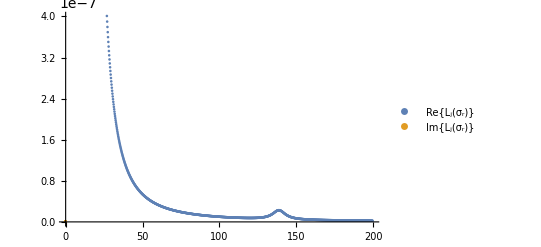

```mathematica
sigmaI=5;
smin=10.1;smax=200;nbrs=1000;
sigmaRange=Range[smin,smax,(smax-smin)/nbrs];

lOfSigma={};
For[n=1,n<nbrs,n++,(
(*Subscript[σ, r]=n;Subscript[σ, i]=5;σ=Subscript[σ, r]+I Subscript[σ, i];*)
coeff=LinearSolve[ham-Conjugate[sigmaRange[[n]]+sigmaI I] norm,RHS];
lOfSigma=Append[lOfSigma,{sigmaRange[[n]],Conjugate[coeff].norm.coeff}];
)]
ListPlot[{Re[lOfSigma],Im[lOfSigma]},PlotLegends->{"Re{L_j(σ_r)}","Im{L_j(σ_r)}"},PlotRange->{0,4 10^(-7)}](*,PlotRange->{0,10^(-6)}]*)
```

```mathematica
ϕ=Pi/3;
θ=Pi/3;
Plot[Re[expandedState[r Cos[θ] Sin[ϕ],r Sin[θ] Sin[ϕ],r Cos[ϕ],Lsets[[jj+1]],basisWidths,coeff]],{r,.01,6.5}]
```

```mathematica
basisWidths//MatrixForm
```

({12.9567,5.13467,2.939,1.69017,0.843,0.257369,0.13852,0.038519}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011})

```mathematica
normmalcoeff=norm.coeff
normmalcoeff.coeff//MatrixForm
Conjugate[coeff].norm.coeff
```

{1.05785×10^-6+3.06049×10^-8 ⅈ,2.41402×10^-8+7.40847×10^-10 ⅈ,8.60316×10^-8+2.53363×10^-9 ⅈ,1.86044×10^-7+5.42301×10^-9 ⅈ,3.68715×10^-7+1.07022×10^-8 ⅈ,8.94637×10^-7+2.58962×10^-8 ⅈ}

1.36588×10^-12+7.91869×10^-14 ⅈ

1.36817×10^-12-1.31266×10^-27 ⅈ

```mathematica
ell=1;
m1=4;
m2=4;
(2 ell+1)!!/(2^(2+ell) (basisWidths[[ell+1]][[m1]]+basisWidths[[ell+1]][[m2]])^(1+ell)) Sqrt[Pi/(basisWidths[[ell+1]][[m1]]+basisWidths[[ell+1]][[m2]])]
```

0.0768279